## cylindrical nanoscale mosfet compact model -- potential distribution

### physical parameter

```mathematica
e=1.60218 10^-19;(*unit charge[C]*)
kB=1.38066 10^-23;(*Boltzmann constant[J/K]*)h=6.62607 10^-34;(*Planck's constant[Js]*)
hbar=h/(2 π);(*[Js]*)
T=300;(*temperature[K]*)
ϵ0=8.85418 10^-12;(*permittivity in vaccum[F/m]*)vt=(kB T)/e;(*thermal voltage[V]*)
m0=9.10938 10^-31;(*effective mass of electron in vaccum[kg]*)nm=10^-9;
ϵox=3.9 ϵ0;(*permittivity of oxide[F/m]*)
ϵsi=11.8 ϵ0;(*permittivity of silicon according to SILVACO[F/m]*)mt=0.19 m0;(*transverse effective mass of electron in SILICON[kg]*)
ml=0.916 m0;(*longitudinal effective mass of electron in SILICON[kg]*)
mr=2 (ml^-1+mt^-1)^-1;(*effective mass along radius direction in cross section in SILICON[kg]*)
GWF=4.5;(*workfunction of gate material from SILVACO[eV]*)CEA=4.17;(*electron affinity of channel material from SILVACO[eV]*)
wgc=GWF-CEA;(*workfunction difference between gate and channel[V]*)
wfb=0;(*conduction band edge under flat-band condition*)vbi=0.19;(*built-in voltage*)
Eg=0.54;(*fitting parameter*)
```

### device parameter

```mathematica
R=2 nm;(*radius of cross-section*)
Tox=0.5 nm;(*oxide thickness*)Cox[r_,tox_]:=2 π (ϵox)/Log[1+tox/r];(*capacitance of cylinder per unit length (F/m)*)
L1=5 nm;
L2=7 nm;
L3=10 nm;
L4=12 nm;
L=7 nm;(*Length of channel*)
```

### bias parameter

```mathematica
VGS0=0;
VGS2=0.2;
VGS5=0.5;
VGS8=0.8;
VDS=0.6;
```

### subband parameter

```mathematica
besselenergylevel[nf_,nr_,m_,r_]:=hbar^2/(2 m) (BesselJZero[nf,nr]/r)^2
besselelement[νf_,νr_,nf_,nr_]:=1/(2 Pi) Integrate[BesselJ[νf,BesselJZero[νf,νr] ζ]^2 ζ,{ζ,0,1}]^-.5 Integrate[BesselJ[nf,BesselJZero[nf,nr] ζ]^2 ζ,{ζ,0,1}]^-.5 Integrate[Exp[I (nf-νf) ϕ],{ϕ,0,2 Pi}] Integrate[BesselJ[νf,BesselJZero[νf,νr] ζ] (1-ζ^2) BesselJ[nf,BesselJZero[nf,nr] ζ] ζ,{ζ,0,1}]
valleykxky=4;(*4-fold degeneracy*)valleykz=2;(*2-fold degeneracy*)subbandtable={{valleykxky,mt/m0,besselenergylevel[0,1,mr,R]/e,besselenergylevel[0,1,mr,R]/(kB T),besselelement[0,1,0,1],0,besselenergylevel[0,1,mr,R]/e},{valleykz,ml/m0,besselenergylevel[0,1,mt,R]/e,besselenergylevel[0,1,mt,R]/(kB T),besselelement[0,1,0,1],0,besselenergylevel[0,1,mt,R]/e},{valleykxky,mt/m0,besselenergylevel[1,1,mr,R]/e,besselenergylevel[1,1,mr,R]/(kB T),besselelement[1,1,1,1],0,besselenergylevel[1,1,mr,R]/e},{valleykz,ml/m0,besselenergylevel[1,1,mt,R]/e,besselenergylevel[1,1,mt,R]/(kB T),besselelement[1,1,1,1],0,besselenergylevel[1,1,mt,R]/e},{valleykxky,mt/m0,besselenergylevel[0,2,mr,R]/e,besselenergylevel[0,2,mr,R]/(kB T),besselelement[0,2,0,2],0,besselenergylevel[0,2,mr,R]/e},{valleykz,ml/m0,besselenergylevel[0,2,mt,R]/e,besselenergylevel[0,2,mt,R]/(kB T),besselelement[0,2,0,2],0,besselenergylevel[0,2,mt,R]/e},{valleykxky,mt/m0,besselenergylevel[1,2,mr,R]/e,besselenergylevel[1,2,mr,R]/(kB T),besselelement[1,2,1,2],0,besselenergylevel[1,2,mr,R]/e},{valleykz,ml/m0,besselenergylevel[1,2,mt,R]/e,besselenergylevel[1,2,mt,R]/(kB T),besselelement[1,2,1,2],0,besselenergylevel[0,2,mt,R]/e},{valleykxky,mt/m0,besselenergylevel[2,2,mr,R]/e,besselenergylevel[2,2,mr,R]/(kB T),besselelement[2,2,2,2],0,besselenergylevel[2,2,mr,R]/e},{valleykz,ml/m0,besselenergylevel[2,2,mt,R]/e,besselenergylevel[2,2,mt,R]/(kB T),besselelement[2,2,2,2],0,besselenergylevel[2,2,mt,R]/e}}(*gnv,mc,Eq0/e,Eq0/kBT,H0xx,reflection*)
```

{{4,0.19,0.175027,6.77031,0.781943,0,0.175027},{2,0.916,0.289918,11.2145,0.781943,0,0.289918},{4,0.19,0.444347,17.188,0.666667,0,0.444347},{2,0.916,0.736026,28.4706,0.666667,0,0.736026},{4,0.19,0.922208,35.6724,0.688545,0,0.922208},{2,0.916,1.52756,59.0884,0.688545,0,1.52756},{4,0.19,1.48959,57.6195,0.666667,0,1.48959},{2,0.916,2.46738,95.4421,0.666667,0,1.52756},{4,0.19,2.14426,82.9433,0.638438,0,2.14426},{2,0.916,3.5518,137.389,0.638438,0,3.5518}}

### Fermi Integral

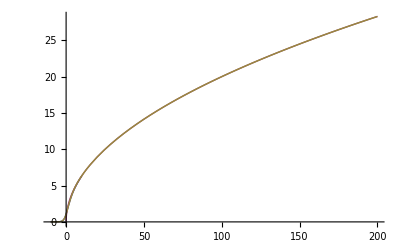

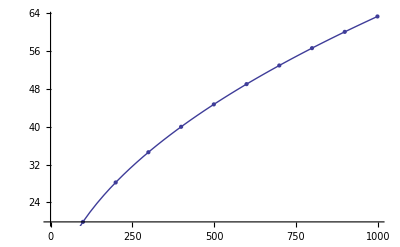

```mathematica
fermiintegral[j_,ζ_]:=-Gamma[1+j] PolyLog[1+j,-Exp[ζ]]
fermiintegralappro[j_,ζ_]:=1/(j+1) ζ^(j+1)
fermiintegralaymerich[j_,ξ_]:=(((j+1) 2^(j+1))/(b+ξ+(Abs[ξ-b]^c+a^c)^(1/c))^(j+1)+Exp[-ξ]/Gamma[j+1])^-1/.a->(1+15/4 (j+1)+1/40 (j+1)^2)^(1/2)/.b->1.8+0.61 j/.c->2+(2-Sqrt[2]) 2^-j
Plot[{fermiintegral[-0.5,x],fermiintegralappro[-.5,x],fermiintegralaymerich[-.5,x]},{x,-10,200}]
Show[ListPlot[Table[{x,fermiintegralappro[-.5,x]},{x,-1,1000,100}]],Plot[fermiintegralaymerich[-.5,x],{x,-1,1000}]]
```

## calculation of 1st subband about ΔUG

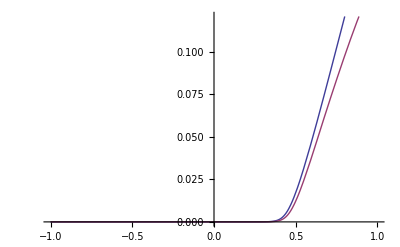

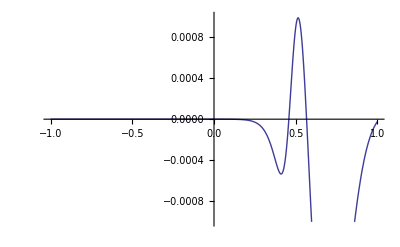

```mathematica
lowestsubbandnumug[r_,tox_,st_,vgs_,vds_,WGC_,WFB_]:=Re[FindRoot[4 Pi ϵsi U==e/(Pi hbar) Sqrt[(kB T mt)/2] st[[1,1]] (fermiintegralaymerich[-0.5,(vgs-wgc+wfb-(4 Pi ϵsi U)/Cox[r,tox])/vt-Eq01]+fermiintegralaymerich[-0.5,(vgs-wgc+wfb-(4 Pi ϵsi U)/Cox[r,tox])/vt-Eq01-vds/vt])/.Eq01->st[[1,4]]+st[[1,5]] U/vt,{U,0.01}][[1,2]]]
Plot[{lowestsubbandnumug[R,Tox,subbandtable,vgs,0,wgc,0],lowestsubbandnumug[R,Tox,subbandtable,vgs,0.8,wgc,0]},{vgs,-1,1}]
Plot[lowestsubbandnumug[R,Tox,subbandtable,vgs,0.8,wgc,0]-U[vgs],{vgs,-1,1},PlotRange->{-0.001,0.001}]
```

## numerical potential distribution along channel

### characteristic parameter for Bessel function

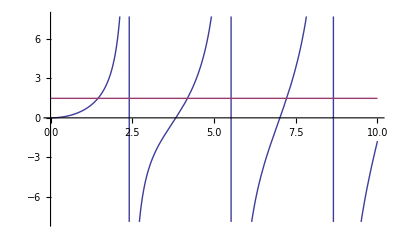

```mathematica
Cr=Cox[R,Tox]/(2 π ϵsi);
FindRoot[BesselJ[1,Λ]/BesselJ[0,Λ] Λ==Cr,{Λ,{2,3,6,10}}];
Plot[{BesselJ[1,Λ]/BesselJ[0,Λ] Λ,Cr},{Λ,0,10}]
λ1=Max[FindRoot[BesselJ[1,Λ]/BesselJ[0,Λ] Λ==Cr,{Λ,{1}}][[1]][[2]]];
```

### characteristic function along channel

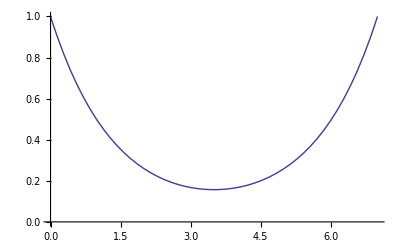

Export::nodir: 目录 "C:\\home\\tei\\mathematica\\" 不存在.

OpenWrite::noopen: 无法打开 "C:\\home\\tei\\mathematica\\Sfunction.txt".

```mathematica
s[z_]:=Exp[-λ1/R z]+(1-Exp[-λ1/R L]) Sinh[λ1/R z]/Sinh[λ1/R L]
Plot[s[z],{z,0,L},PlotRange->{0,1}]
Table[{z,s[z]},{z,0 nm,11 nm,0.01 nm}];
Export["/home/tei/mathematica/Sfunction.txt",Table[{z,s[z]},{z,0,L,.01 nm}]];
```

### numerical potential distribution along channel only

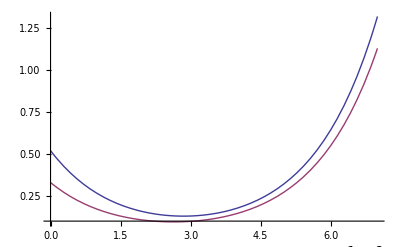

```mathematica
numΦ[r_,tox_,st_,z_,vgs_,vds_,VBI_,WGC_,WFB_]:=(VBI-w0) s[z]+vds Sinh[λ1/R z]/Sinh[λ1/R L]/.w0->ws-lowestsubbandnumug[R,tox,st,vgs,vds,WGC,WFB] (1-r^2/R^2)/.ws->vgs-WGC+WFB-(4 π ϵsi lowestsubbandnumug[R,tox,st,vgs,vds,WGC,WFB])/Cox[R,Tox]
Plot[{numΦ[0,Tox,subbandtable,z,VGS0,0.8,vbi,wgc,0],numΦ[0,Tox,subbandtable,z,VGS0,0.8,0,wgc,0](*,Φ2D[0,z,0,0.8]*)},{z,0,L}]
```

### numerical potential distribution

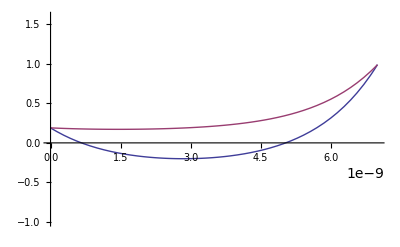

```mathematica
numnΦ2D[r_,tox_,st_,z_,vgs_,vds_,VBI_,WGC_,WFB_]:=numΦ[r,tox,st,z,vgs,vds,VBI,WGC,WFB]+w0/.w0->ws-lowestsubbandnumug[R,tox,st,vgs,vds,WGC,WFB] (1-r^2/R^2)/.ws->vgs-WGC+WFB-(4 π ϵsi lowestsubbandnumug[R,tox,st,vgs,vds,WGC,WFB])/Cox[R,Tox]
Plot[{numnΦ2D[0,Tox,subbandtable,z,VGS0,0.8,vbi,wgc,0],numnΦ2D[0,Tox,subbandtable,z,VGS5,0.8,vbi,wgc,0]},{z,0,L},PlotRange->{-1,1.6}]
```

### plot of WGC independece

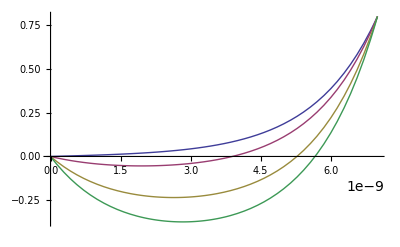

```mathematica
CHECKFORwgcINDEPENDENCE=Plot[{numnΦ2D[0,Tox,subbandtable,z,VGS0,0.8,0,0,0],numnΦ2D[0,Tox,subbandtable,z,VGS0,0.8,0,.1,0],numnΦ2D[0,Tox,subbandtable,z,VGS0,0.8,0,wgc,0],numnΦ2D[0,Tox,subbandtable,z,VGS0,0.8,0,.5,0]},{z,0,L}]
```

### plot of VBI independence

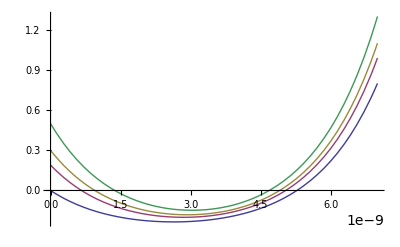

```mathematica
CHECKFORvbiINDEPECDENCE=Plot[{numnΦ2D[0,Tox,subbandtable,z,VGS0,0.8,0,wgc,0],numnΦ2D[0,Tox,subbandtable,z,VGS0,0.8,vbi,wgc,0],numnΦ2D[0,Tox,subbandtable,z,VGS0,0.8,.3,wgc,0],numnΦ2D[0,Tox,subbandtable,z,VGS0,0.8,0.5,wgc,0]},{z,0,L}]
```

### plot of numerical potential distribution

```mathematica
numvgr2nmL1D00vd08=ListPlot[{Table[{10^9 z+9,Re[numnΦ2D[0,Tox,subbandtable,z,VGS0,0.8,vbi,wgc,0]]},{z,0,L,1 nm}]}];
numvgr2nmL1D02vd08=ListPlot[{Table[{10^9 z+9,Re[numnΦ2D[0,Tox,subbandtable,z,VGS2,0.8,vbi,wgc,0]]},{z,0,L,1 nm}]}];
numvgr2nmL1D05vd08=ListPlot[{Table[{10^9 z+9,Re[numnΦ2D[0,Tox,subbandtable,z,VGS5,0.8,vbi,wgc,0]]},{z,0,L,1 nm}]}];
numvgr2nmL1D08vd08=ListPlot[{Table[{10^9 z+9,Re[numnΦ2D[0,Tox,subbandtable,z,VGS8,0.8,vbi,wgc,0]]},{z,0,L,1 nm}]}];
numvgr2nmL1D00vd00=ListPlot[{Table[{10^9 z+9,Re[numnΦ2D[0,Tox,subbandtable,z,VGS0,0.,vbi,wgc,0]]},{z,0,L,1 nm}]}];
Export["/home/tei/mathematica/numchannelelectricpotentialdistribution.txt",Table[{10^9 z,numnΦ2D[0,Tox,subbandtable,z,VGS0,0.8,vbi,wgc,0],numnΦ2D[0,Tox,subbandtable,z,VGS2,0.8,vbi,wgc,0],numnΦ2D[0,Tox,subbandtable,z,VGS5,0.8,vbi,wgc,0],numnΦ2D[0,Tox,subbandtable,z,VGS8,0.8,vbi,wgc,0]},{z,0,L,0.1 nm}],"CSV"];
```

Export::nodir: 目录 "C:\\home\\tei\\mathematica\\" 不存在.

OpenWrite::noopen: 无法打开 "C:\\home\\tei\\mathematica\\numchannelelectricpotentialdistribution.txt".

### energy level distribution

```mathematica
Eq01[r_,tox_,st_,vgs_,vds_,z_,VBI_,WGC_,WFB_]:=-e ((VBI-w0) s[z]+vds Sinh[λ1/R z]/Sinh[λ1/R L]+w0)+kB T subbandtable[[1,4]]+subbandtable[[1,5]] e lowestsubbandnumug[r,tox,st,vgs,vds]/.w0->ws-lowestsubbandnumug[R,tox,st,vgs,vds,WGC,WFB] (1-r^2/R^2)/.ws->vgs-WGC+WFB-(4 π ϵsi lowestsubbandnumug[R,tox,st,vgs,vds,WGC,WFB])/Cox[R,Tox]
Plot[{Eq01[R,Tox,subbandtable,VGS0,VDS,z,vbi,wgc,wfb]/e,Eq01[R,Tox,subbandtable,VGS2,VDS,z,vbi,wgc,wfb]/Eq01[R,Tox,subbandtable,VGS5,VDS,z,vbi,wgc,wfb]/e(*,(Eq01[R,Tox,subbandtable,VGS8,VDS,z,vbi,wgc,wfb]/e)*)},{z,0,L}]
FirstsubbandVG00VD08=ListPlot[Table[{10^9 z+9.25,Eq01[R,Tox,subbandtable,VGS0,VDS,z,vbi,wgc,wfb]/e},{z,0,L,1 nm}]];
FirstsubbandVG02VD08=ListPlot[Table[{10^9 z+9.25,Eq01[R,Tox,subbandtable,VGS2,VDS,z,vbi,wgc,wfb]/e},{z,0,L,1 nm}]];
FirstsubbandVG05VD08=ListPlot[Table[{10^9 z+9.25,Eq01[R,Tox,subbandtable,VGS5,VDS,z,vbi,wgc,wfb]/e},{z,0,L,1 nm}]];
FirstsubbandVG08VD08=ListPlot[Table[{10^9 z+9.25,Eq01[R,Tox,subbandtable,VGS8,VDS,z,vbi,wgc,wfb]/e},{z,0,L,1 nm}]];
```

-Graphics-

### SILVACO result

```mathematica
SILVACOFirstsubbandvg02vd08=Import["/home/tei/mathematica/silvaco_r2nm_L1D/1stsubband_silvaco_r2nmL10nm_vg02vd08.txt","Table"];
SILVACOFirstsubbandvg00vd08=Import["/home/tei/mathematica/silvaco_r2nm_L1D/1stsubband_silvaco_r2nmL10nm_vg00vd08.txt","Table"];
SILVACOFirstsubbandvg05vd08=Import["/home/tei/mathematica/silvaco_r2nm_L1D/1stsubband_silvaco_r2nmL10nm_vg05vd08.txt","Table"];
SILVACOFirstsubbandvg08vd08=Import["/home/tei/mathematica/silvaco_r2nm_L1D/1stsubband_silvaco_r2nmL10nm_vg08vd08.txt","Table"];
SILVACOFirstsubbandr2nmL1Dnm01=Show[ListLinePlot[SILVACOFirstsubbandvg02vd08],ListLinePlot[SILVACOFirstsubbandvg00vd08],ListLinePlot[SILVACOFirstsubbandvg05vd08],ListLinePlot[SILVACOFirstsubbandvg08vd08],PlotRange->{-0.9,0.5}]
Show[SILVACOFirstsubbandr2nmL1Dnm01,FirstsubbandVG00VD08,FirstsubbandVG02VD08,FirstsubbandVG05VD08,FirstsubbandVG08VD08]
Export["/home/tei/mathematica/channelpotentialdistribution.txt",Table[{10^9 z,Eq01[R,Tox,subbandtable,VGS0,VDS,z,vbi,wgc,wfb]/e,Eq01[R,Tox,subbandtable,VGS2,VDS,z,vbi,wgc,wfb]/e,Eq01[R,Tox,subbandtable,VGS5,VDS,z,vbi,wgc,wfb]/e,Eq01[R,Tox,subbandtable,VGS8,VDS,z,vbi,wgc,wfb]/e},{z,0,L,0.1 nm}],"CSV"]
Export["E:\data_for_mathematica\\channelpotentialdistributionL20nm.txt",Table[{10^9 z,Eq01[R,Tox,subbandtable,VGS0,VDS,z,vbi,wgc,wfb]/e},{z,0,L,0.1 nm}],"CSV"]
```

Import::nffil: 在 Import 中未找到文件.

ListLinePlot::lpn: $Failed 不是由数字或者数对组成的列表.

General::stop: 在本次计算中，ListLinePlot :: lpn 的进一步输出将被抑制.

Show::gcomb: 无法合并 Show[ListLinePlot[$Failed], ListLinePlot[$Failed], ListLinePlot[$Failed], ListLinePlot[$Failed], PlotRange → {-0.9, 0.5}] 中的图形对象.

Show[ListLinePlot[$Failed],ListLinePlot[$Failed],ListLinePlot[$Failed],ListLinePlot[$Failed],PlotRange→{-0.9,0.5}]

Show::gcomb: 无法合并 Show[ListLinePlot[$Failed], ListLinePlot[$Failed], ListLinePlot[$Failed], ListLinePlot[$Failed], PlotRange → {-0.9`, 0.5`}], GraphicsBox[List[List[], List[], List[]], List[Rule[AxesLabel, List[None, None]], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[Method, List[]], Rule[PlotRange, List[List[-1, 1], List[-1, 1]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[List[0.04`, 0.04`], List[0.04`, 0.04`]]]]], GraphicsBox[List[List[], List[], List[]], List[Rule[AxesLabel, List[None, None]], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[Method, List[]], Rule[PlotRange, List[List[-1, 1], List[-1, 1]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[List[0.04`, 0.04`], List[0.04`, 0.04`]]]]], GraphicsBox[List[List[], List[], List[]], List[Rule[AxesLabel, List[None, None]], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[Method, List[]], Rule[PlotRange, List[List[-1, 1], List[-1, 1]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[List[0.04`, 0.04`], List[0.04`, 0.04`]]]]], GraphicsBox[List[List[], List[], List[]], List[Rule[AxesLabel, List[None, None]], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[Method, List[]], Rule[PlotRange, List[List[-1, 1], List[-1, 1]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[List[0.04`, 0.04`], List[0.04`, 0.04`]]]]] 中的图形对象.

Show[Show[ListLinePlot[$Failed],ListLinePlot[$Failed],ListLinePlot[$Failed],ListLinePlot[$Failed],PlotRange→{-0.9,0.5}],-Graphics-,-Graphics-,-Graphics-,-Graphics-]

Export::nodir: 目录 "C:\\home\\tei\\mathematica\\" 不存在.

OpenWrite::noopen: 无法打开 "C:\\home\\tei\\mathematica\\channelpotentialdistribution.txt".

$Failed

E:\data_for_mathematica\channelpotentialdistributionL20nm.txt

## analytic potential distribution along channel

### characteristic parameter

```mathematica
γ=Sqrt[4/α]/.α->((4 π ϵsi)/Cox[R,Tox]+1) R^2;
ugzero[vbi_,vgs_]:=(vbi-vgs+wgc-wfb)/-(α/R^2)/.α->((4 π ϵsi)/Cox[R,Tox]+1) R^2
ugLg[vbi_,vgs_,vds_]:=(vbi-vgs+wgc-wfb+vds)/-(α/R^2)/.α->((4 π ϵsi)/Cox[R,Tox]+1) R^2
```

### ΔUG along channel

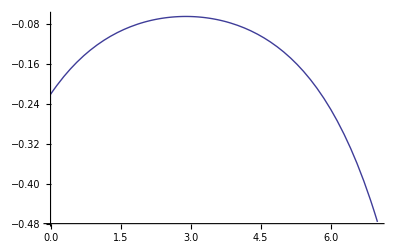

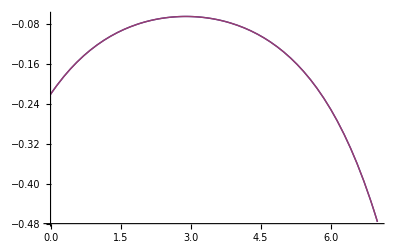

```mathematica
ug[vbi_,vgs_,vds_,z_]:=1/Sinh[γ L] (ugzero[vbi,vgs] Sinh[γ (L-z)]+ugLg[vbi,vgs,vds] Sinh[γ z])
aug[vbi_,vgs_,vds_,z_]:=-(vbi-vgs+wgc-wfb) (Sinh[γ (L-z)]+Sinh[γ z])/(Sinh[γ L] ((4 π ϵsi)/Cox[R,Tox]+1))-vds Sinh[γ z]/(Sinh[γ L] ((4 π ϵsi)/Cox[R,Tox]+1))
Plot[aug[vbi,VGS0,VDS,z],{z,0,L}]
Plot[{ug[vbi,VGS0,VDS,z],aug[vbi,VGS0,VDS,z]},{z,0,L}]
```

### potential distribution

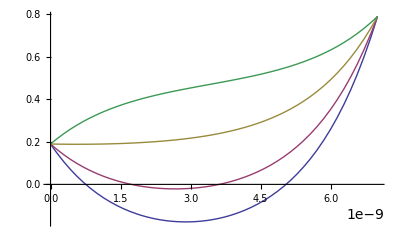

```mathematica
ϕ[vbi_,vgs_,vds_,r_,z_]:=WS-ug[vbi,vgs,vds,z] (1-r^2/R^2)/.WS->vgs-wgc+wfb-(4 π ϵsi)/Cox[R,Tox] ug[vbi,vgs,vds,z]
Plot[{ϕ[vbi,VGS0,VDS,0,z],ϕ[vbi,VGS2,VDS,0,z],ϕ[vbi,VGS5,VDS,0,z],ϕ[vbi,VGS8,VDS,0,z]},{z,0,L}]
POTENTIALPLOTVG00VD08=ListPlot[Table[{10^9 z+9.25,ϕ[vbi,VGS0,VDS,0,z]+0.54},{z,0,L,1 nm}]];
POTENTIALPLOTVG02VD08=ListPlot[Table[{10^9 z+9.25,ϕ[vbi,VGS2,VDS,0,z]+0.54},{z,0,L,1 nm}]];
POTENTIALPLOTVG05VD08=ListPlot[Table[{10^9 z+9.25,ϕ[vbi,VGS5,VDS,0,z]+0.54},{z,0,L,1 nm}]];
POTENTIALPLOTVG08VD08=ListPlot[Table[{10^9 z+9.25,ϕ[vbi,VGS8,VDS,0,z]+0.54},{z,0,L,1 nm}]];
```

### SILVACO result

Import::nffil: 在 Import 中未找到文件.

ListLinePlot::lpn: $Failed 不是由数字或者数对组成的列表.

General::stop: 在本次计算中，ListLinePlot :: lpn 的进一步输出将被抑制.

Show::gcomb: 无法合并 Show[ListLinePlot[$Failed], ListLinePlot[$Failed], ListLinePlot[$Failed], ListLinePlot[$Failed]] 中的图形对象.

Show[ListLinePlot[$Failed],ListLinePlot[$Failed],ListLinePlot[$Failed],ListLinePlot[$Failed]]

Show::gcomb: 无法合并 Show[ListLinePlot[$Failed], ListLinePlot[$Failed], ListLinePlot[$Failed], ListLinePlot[$Failed]], GraphicsBox[List[List[], List[Hue[0.67`, 0.6`, 0.6`], Directive[RGBColor[0.24720000000000014`, 0.24`, 0.6`]], PointBox[List[List[9.25`, 0.7299999999999999`], List[10.25`, 0.49706261296685283`], List[11.25`, 0.3906561778305463`], List[12.25`, 0.36387905391207986`], List[13.25`, 0.4049284677905398`], List[14.25`, 0.5318981076657499`], List[15.25`, 0.8007534273088163`], List[16.25`, 1.33`]]]], List[]], List[Rule[AxesLabel, List[None, None]], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesOrigin, List[9.25`, 0.36387905391207986`]], Rule[Method, List[]], Rule[PlotRange, List[List[9.25`, 16.25`], List[0.36387905391207986`, 1.33`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[List[0.14`, 0.14`], List[0.019322418921758403`, 0.019322418921758403`]]]]], GraphicsBox[List[List[], List[Hue[0.67`, 0.6`, 0.6`], Directive[RGBColor[0.24720000000000014`, 0.24`, 0.6`]], PointBox[List[List[9.25`, 0.73`], List[10.25`, 0.5900118763478688`], List[11.25`, 0.5293690698431931`], List[12.25`, 0.5213415512654189`], List[13.25`, 0.5623909651438789`], List[14.25`, 0.6706109996783967`], List[15.25`, 0.8937026906898322`], List[16.25`, 1.33`]]]], List[]], List[Rule[AxesLabel, List[None, None]], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesOrigin, List[9.25`, 0.5213415512654189`]], Rule[Method, List[]], Rule[PlotRange, List[List[9.25`, 16.25`], List[0.5213415512654189`, 1.33`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[List[0.14`, 0.14`], List[0.016173168974691624`, 0.016173168974691624`]]]]], GraphicsBox[List[List[], List[Hue[0.67`, 0.6`, 0.6`], Directive[RGBColor[0.24720000000000014`, 0.24`, 0.6`]], PointBox[List[List[9.25`, 0.73`], List[10.25`, 0.7294357714193928`], List[11.25`, 0.7374384078621633`], List[12.25`, 0.7575352972954275`], List[13.25`, 0.7985847111738875`], List[14.25`, 0.8786803376973669`], List[15.25`, 1.0331265857613563`], List[16.25`, 1.33`]]]], List[]], List[Rule[AxesLabel, List[None, None]], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesOrigin, List[9.25`, 0.7294357714193928`]], Rule[Method, List[]], Rule[PlotRange, List[List[9.25`, 16.25`], List[0.7294357714193928`, 1.33`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[List[0.14`, 0.14`], List[0.012011284571612147`, 0.012011284571612147`]]]]], GraphicsBox[List[List[], List[Hue[0.67`, 0.6`, 0.6`], Directive[RGBColor[0.24720000000000014`, 0.24`, 0.6`]], PointBox[List[List[9.25`, 0.73`], List[10.25`, 0.8688596664909167`], List[11.25`, 0.9455077458811335`], List[12.25`, 0.9937290433254361`], List[13.25`, 1.034778457203896`], List[14.25`, 1.086749675716337`], List[15.25`, 1.17255048083288`], List[16.25`, 1.33`]]]], List[]], List[Rule[AxesLabel, List[None, None]], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesOrigin, List[9.25`, 0.73`]], Rule[Method, List[]], Rule[PlotRange, List[List[9.25`, 16.25`], List[0.73`, 1.33`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[List[0.14`, 0.14`], List[0.012000000000000002`, 0.012000000000000002`]]]]] 中的图形对象.

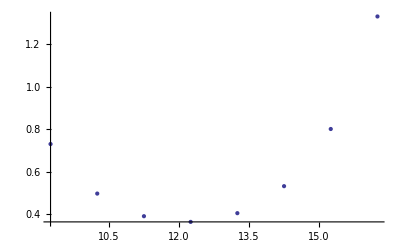
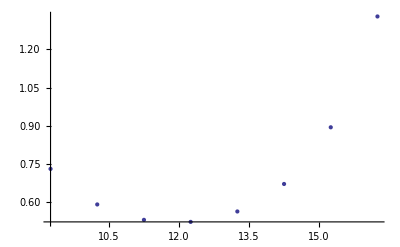
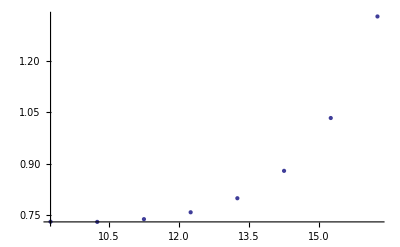
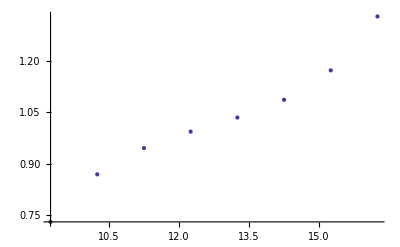
Show[Show[ListLinePlot[$Failed],ListLinePlot[$Failed],ListLinePlot[$Failed],ListLinePlot[$Failed]],-Graphics-,-Graphics-,-Graphics-,-Graphics-]

```mathematica
SILVACOQWR2nmL1Dnmvg00vd08=Import["/home/tei/mathematica/silvaco_r2nm_L1D/Qr2nmL10nm_vg0vd08.txt","Table"];
SILVACOQWR2nmL1Dnmvg02vd08=Import["/home/tei/mathematica/silvaco_r2nm_L1D/Qr2nmL10nm_vg02vd08.txt","Table"];
SILVACOQWR2nmL1Dnmvg05vd08=Import["/home/tei/mathematica/silvaco_r2nm_L1D/Qr2nmL10nm_vg05vd08.txt","Table"];
SILVACOQWR2nmL1Dnmvg08vd08=Import["/home/tei/mathematica/silvaco_r2nm_L1D/Qr2nmL10nm_vg08vd08.txt","Table"];
silvacoresultquantumr2nmL1Dnm=Show[ListLinePlot[SILVACOQWR2nmL1Dnmvg00vd08],ListLinePlot[SILVACOQWR2nmL1Dnmvg02vd08],ListLinePlot[SILVACOQWR2nmL1Dnmvg05vd08],ListLinePlot[SILVACOQWR2nmL1Dnmvg08vd08]]
Show[silvacoresultquantumr2nmL1Dnm,POTENTIALPLOTVG00VD08,POTENTIALPLOTVG02VD08,POTENTIALPLOTVG05VD08,POTENTIALPLOTVG08VD08]
Export["E:\data_for_mathematica\\electrostaticpotentialdistribution.txt",Table[Re[{10^9 z,ϕ[vbi,VGS0,VDS,0,z],ϕ[vbi,VGS2,VDS,0,z],ϕ[vbi,VGS5,VDS,0,z],ϕ[vbi,VGS8,VDS,0,z]}],{z,0,L,0.1 nm}],"CSV"];
```

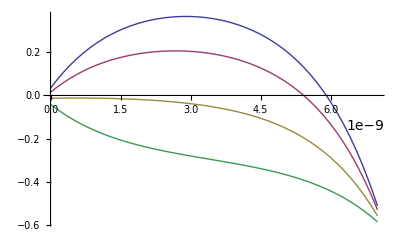

ListLinePlot::lpn: $Failed 不是由数字或者数对组成的列表.

General::stop: 在本次计算中，ListLinePlot :: lpn 的进一步输出将被抑制.

Show::gcomb: 无法合并 Show[ListLinePlot[$Failed], ListLinePlot[$Failed], ListLinePlot[$Failed], ListLinePlot[$Failed], PlotRange → {-1, 0.5}] 中的图形对象.

Show[ListLinePlot[$Failed],ListLinePlot[$Failed],ListLinePlot[$Failed],ListLinePlot[$Failed],PlotRange→{-1,0.5}]

Show::gcomb: 无法合并 Show[ListLinePlot[$Failed], ListLinePlot[$Failed], ListLinePlot[$Failed], ListLinePlot[$Failed], PlotRange → {-1, 0.5`}], GraphicsBox[List[List[], List[Hue[0.67`, 0.6`, 0.6`], Directive[RGBColor[0.24720000000000014`, 0.24`, 0.6`]], PointBox[List[List[9.25`, 0.03327171734742552`], List[10.25`, 0.24459763318940503`], List[11.25`, 0.34113188921014564`], List[12.25`, 0.3654246844018375`], List[13.25`, 0.32818375415388384`], List[14.25`, 0.2129941069593917`], List[15.25`, -0.030917346569853114`], List[16.25`, -0.5110614664327494`]]]], List[]], List[Rule[AxesLabel, List[None, None]], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesOrigin, List[9.25`, 0.`]], Rule[Method, List[]], Rule[PlotRange, List[List[9.25`, 16.25`], List[-0.5110614664327494`, 0.3654246844018375`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[List[0.14`, 0.14`], List[0.01752972301669174`, 0.01752972301669174`]]]]], GraphicsBox[List[List[], List[Hue[0.67`, 0.6`, 0.6`], Directive[RGBColor[0.24720000000000014`, 0.24`, 0.6`]], PointBox[List[List[9.25`, 0.014716111940816923`], List[10.25`, 0.14171641367244583`], List[11.25`, 0.19673290023587126`], List[12.25`, 0.20401564147802845`], List[13.25`, 0.16677471123007476`], List[14.25`, 0.06859511798511723`], List[15.25`, -0.1337985660868123`], List[16.25`, -0.5296170718393578`]]]], List[]], List[Rule[AxesLabel, List[None, None]], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesOrigin, List[9.25`, 0.`]], Rule[Method, List[]], Rule[PlotRange, List[List[9.25`, 16.25`], List[-0.5296170718393578`, 0.20401564147802845`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[List[0.14`, 0.14`], List[0.014672654266347725`, 0.014672654266347725`]]]]], GraphicsBox[List[List[], List[Hue[0.67`, 0.6`, 0.6`], Directive[RGBColor[0.24720000000000014`, 0.24`, 0.6`]], PointBox[List[List[9.25`, -0.013117296169095741`], List[10.25`, -0.012605415602992873`], List[11.25`, -0.01986558322554043`], List[12.25`, -0.038097922907685156`], List[13.25`, -0.07533885315563885`], List[14.25`, -0.1480033654762944`], List[15.25`, -0.2881203953622511`], List[16.25`, -0.5574504799492704`]]]], List[]], List[Rule[AxesLabel, List[None, None]], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesOrigin, List[9.25`, -0.5574504799492704`]], Rule[Method, List[]], Rule[PlotRange, List[List[9.25`, 16.25`], List[-0.5574504799492704`, 0]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[List[0.14`, 0.14`], List[0.01114900959898541`, 0.01114900959898541`]]]]], GraphicsBox[List[List[], List[Hue[0.67`, 0.6`, 0.6`], Directive[RGBColor[0.24720000000000014`, 0.24`, 0.6`]], PointBox[List[List[9.25`, -0.04095070427900834`], List[10.25`, -0.16692724487843158`], List[11.25`, -0.2364640666869521`], List[12.25`, -0.2802114872933988`], List[13.25`, -0.3174524175413525`], List[14.25`, -0.3646018489377061`], List[15.25`, -0.4424422246376896`], List[16.25`, -0.585283888059183`]]]], List[]], List[Rule[AxesLabel, List[None, None]], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesOrigin, List[9.25`, -0.585283888059183`]], Rule[Method, List[]], Rule[PlotRange, List[List[9.25`, 16.25`], List[-0.585283888059183`, 0]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[List[0.14`, 0.14`], List[0.011705677761183659`, 0.011705677761183659`]]]]], PlotRange → {-1, 0.5`} 中的图形对象.

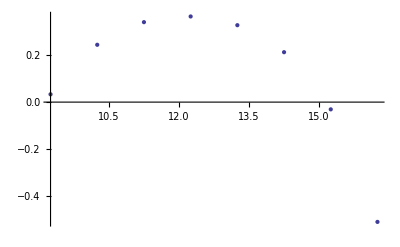
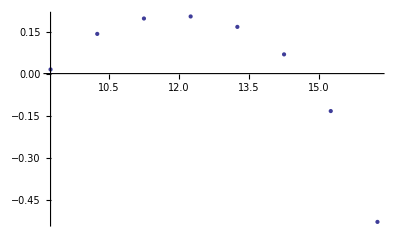
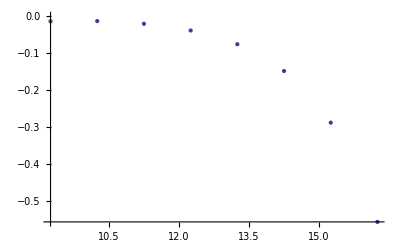
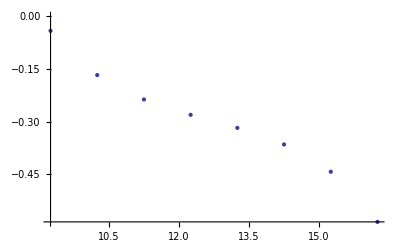
Show[Show[ListLinePlot[$Failed],ListLinePlot[$Failed],ListLinePlot[$Failed],ListLinePlot[$Failed],PlotRange→{-1,0.5}],-Graphics-,-Graphics-,-Graphics-,-Graphics-,PlotRange→{-1,0.5}]

```mathematica
Eq01[vbi_,vgs_,vds_,z_]:=-e WS+kB T subbandtable[[1,4]]+subbandtable[[1,5]] e ug[vbi,vgs,vds,z]/.WS->vgs-wgc+wfb-(4 π ϵsi)/Cox[R,Tox] ug[vbi,vgs,vds,z]
Plot[{Eq01[vbi,VGS0,VDS,z]/e,Eq01[vbi,VGS2,VDS,z]/e,Eq01[vbi,VGS5,VDS,z]/e,Eq01[vbi,VGS8,VDS,z]/e},{z,0,L}]
anotherFirstSubbandVG00VD08=ListPlot[Table[{10^9 z+9.25,Eq01[vbi,VGS0,VDS,z]/e},{z,0,L,1 nm}]];
anotherFirstSubbandVG02VD08=ListPlot[Table[{10^9 z+9.25,Eq01[vbi,VGS2,VDS,z]/e},{z,0,L,1 nm}]];
anotherFirstSubbandVG05VD08=ListPlot[Table[{10^9 z+9.25,Eq01[vbi,VGS5,VDS,z]/e},{z,0,L,1 nm}]];
anotherFirstSubbandVG08VD08=ListPlot[Table[{10^9 z+9.25,Eq01[vbi,VGS8,VDS,z]/e},{z,0,L,1 nm}]];
SILVACOFirstsubbandr2nmL1Dnm02=Show[ListLinePlot[SILVACOFirstsubbandvg02vd08],ListLinePlot[SILVACOFirstsubbandvg00vd08],ListLinePlot[SILVACOFirstsubbandvg05vd08],ListLinePlot[SILVACOFirstsubbandvg08vd08],PlotRange->{-1,0.5}]
Show[SILVACOFirstsubbandr2nmL1Dnm02,anotherFirstSubbandVG00VD08,anotherFirstSubbandVG02VD08,anotherFirstSubbandVG05VD08,anotherFirstSubbandVG08VD08,PlotRange->{-1,0.5}]
Export["E:\data_for_mathematica\\firstsubbanddistributionvg00vd08L7.txt",Table[Re[{10^9 z,Eq01[vbi,VGS0,VDS,z]/e}],{z,0,L,0.1 nm}],"CSV"];
Export["E:\data_for_mathematica\\firstsubbanddistributionvg01vd08.txt",Table[Re[{10^9 z,Eq01[vbi,0.1,VDS,z]/e}],{z,0,L,0.1 nm}],"CSV"];
Export["E:\data_for_mathematica\\firstsubbanddistributionvg02vd08.txt",Table[Re[{10^9 z,Eq01[vbi,VGS2,VDS,z]/e}],{z,0,L,0.1 nm}],"CSV"];
Export["E:\data_for_mathematica\\firstsubbanddistributionvg3vd08.txt",Table[Re[{10^9 z,Eq01[vbi,0.3,VDS,z]/e}],{z,0,L,0.1 nm}],"CSV"];
Export["E:\data_for_mathematica\\firstsubbanddistributionvg04vd08.txt",Table[Re[{10^9 z,Eq01[vbi,0.4,VDS,z]/e}],{z,0,L,0.1 nm}],"CSV"];
Export["E:\data_for_mathematica\\firstsubbanddistributionvg05vd08.txt",Table[Re[{10^9 z,Eq01[vbi,VGS5,VDS,z]/e}],{z,0,L,0.1 nm}],"CSV"];
```

```mathematica
SILVACOQWR1nmL5nmvg00vd08=Import["/home/tei/mathematica/silvaco_r1nmL5nm/vg00vd08.txt","Table"];
SILVACOQWR1nmL5nmvg02vd08=Import["/home/tei/mathematica/silvaco_r1nmL5nm/vg02vd08.txt","Table"];
SILVACOQWR1nmL5nmvg05vd08=Import["/home/tei/mathematica/silvaco_r1nmL5nm/vg05vd08.txt","Table"];
SILVACOQWR1nmL5nmvg08vd08=Import["/home/tei/mathematica/silvaco_r1nmL5nm/vg08vd08.txt","Table"];
silvacoresultquantumr1nmL5nm=Show[ListLinePlot[SILVACOQWR1nmL5nmvg00vd08],ListLinePlot[SILVACOQWR1nmL5nmvg02vd08],ListLinePlot[SILVACOQWR1nmL5nmvg05vd08],ListLinePlot[SILVACOQWR1nmL5nmvg08vd08]]
Show[silvacoresultquantumr1nmL5nm,POTENTIALPLOTVG00VD08,POTENTIALPLOTVG02VD08,POTENTIALPLOTVG05VD08,POTENTIALPLOTVG08VD08]
```

Import::nffil: 在 Import 中未找到文件.

ListLinePlot::lpn: $Failed 不是由数字或者数对组成的列表.

General::stop: 在本次计算中，ListLinePlot :: lpn 的进一步输出将被抑制.

Show::gcomb: 无法合并 Show[ListLinePlot[$Failed], ListLinePlot[$Failed], ListLinePlot[$Failed], ListLinePlot[$Failed]] 中的图形对象.

Show[ListLinePlot[$Failed],ListLinePlot[$Failed],ListLinePlot[$Failed],ListLinePlot[$Failed]]

Show::gcomb: 无法合并 Show[ListLinePlot[$Failed], ListLinePlot[$Failed], ListLinePlot[$Failed], ListLinePlot[$Failed]], GraphicsBox[List[List[], List[Hue[0.67`, 0.6`, 0.6`], Directive[RGBColor[0.24720000000000014`, 0.24`, 0.6`]], PointBox[List[List[9.25`, 0.7299999999999999`], List[10.25`, 0.49706261296685283`], List[11.25`, 0.3906561778305463`], List[12.25`, 0.36387905391207986`], List[13.25`, 0.4049284677905398`], List[14.25`, 0.5318981076657499`], List[15.25`, 0.8007534273088163`], List[16.25`, 1.33`]]]], List[]], List[Rule[AxesLabel, List[None, None]], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesOrigin, List[9.25`, 0.36387905391207986`]], Rule[Method, List[]], Rule[PlotRange, List[List[9.25`, 16.25`], List[0.36387905391207986`, 1.33`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[List[0.14`, 0.14`], List[0.019322418921758403`, 0.019322418921758403`]]]]], GraphicsBox[List[List[], List[Hue[0.67`, 0.6`, 0.6`], Directive[RGBColor[0.24720000000000014`, 0.24`, 0.6`]], PointBox[List[List[9.25`, 0.73`], List[10.25`, 0.5900118763478688`], List[11.25`, 0.5293690698431931`], List[12.25`, 0.5213415512654189`], List[13.25`, 0.5623909651438789`], List[14.25`, 0.6706109996783967`], List[15.25`, 0.8937026906898322`], List[16.25`, 1.33`]]]], List[]], List[Rule[AxesLabel, List[None, None]], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesOrigin, List[9.25`, 0.5213415512654189`]], Rule[Method, List[]], Rule[PlotRange, List[List[9.25`, 16.25`], List[0.5213415512654189`, 1.33`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[List[0.14`, 0.14`], List[0.016173168974691624`, 0.016173168974691624`]]]]], GraphicsBox[List[List[], List[Hue[0.67`, 0.6`, 0.6`], Directive[RGBColor[0.24720000000000014`, 0.24`, 0.6`]], PointBox[List[List[9.25`, 0.73`], List[10.25`, 0.7294357714193928`], List[11.25`, 0.7374384078621633`], List[12.25`, 0.7575352972954275`], List[13.25`, 0.7985847111738875`], List[14.25`, 0.8786803376973669`], List[15.25`, 1.0331265857613563`], List[16.25`, 1.33`]]]], List[]], List[Rule[AxesLabel, List[None, None]], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesOrigin, List[9.25`, 0.7294357714193928`]], Rule[Method, List[]], Rule[PlotRange, List[List[9.25`, 16.25`], List[0.7294357714193928`, 1.33`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[List[0.14`, 0.14`], List[0.012011284571612147`, 0.012011284571612147`]]]]], GraphicsBox[List[List[], List[Hue[0.67`, 0.6`, 0.6`], Directive[RGBColor[0.24720000000000014`, 0.24`, 0.6`]], PointBox[List[List[9.25`, 0.73`], List[10.25`, 0.8688596664909167`], List[11.25`, 0.9455077458811335`], List[12.25`, 0.9937290433254361`], List[13.25`, 1.034778457203896`], List[14.25`, 1.086749675716337`], List[15.25`, 1.17255048083288`], List[16.25`, 1.33`]]]], List[]], List[Rule[AxesLabel, List[None, None]], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesOrigin, List[9.25`, 0.73`]], Rule[Method, List[]], Rule[PlotRange, List[List[9.25`, 16.25`], List[0.73`, 1.33`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[List[0.14`, 0.14`], List[0.012000000000000002`, 0.012000000000000002`]]]]] 中的图形对象.

Show[Show[ListLinePlot[$Failed],ListLinePlot[$Failed],ListLinePlot[$Failed],ListLinePlot[$Failed]],-Graphics-,-Graphics-,-Graphics-,-Graphics-]

## parabolic potential distribution

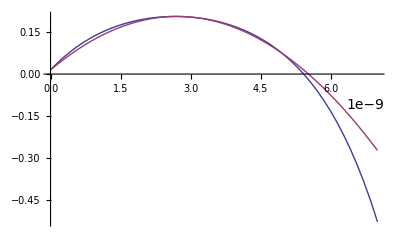

```mathematica
parabolicapproxpotential[vbi_, vgs_, vds_, z_]:=-Abs[Eq01[vbi,vgs,vds,zmax[vbi,vgs,vds]]-Eq01[vbi,vgs,vds,0]]/zmax[vbi,vgs,vds]^2 (z-zmax[vbi,vgs,vds])^2+Eq01[vbi,vgs,vds,zmax[vbi,vgs,vds]]
Plot[{Eq01[vbi,VGS2,VDS,z]/e,parabolicapproxpotential[vbi,VGS2,VDS,z]/e},{z,0,L}]
Export["E:\data_for_mathematica\\paraboapproxfirstsubbanddistributionvg00vg08.txt",Table[Re[{10^9 z,parabolicapproxpotential[vbi,VGS0,VDS,z]/e}],{z,0,L,0.1 nm}],"CSV"];
Export["E:\data_for_mathematica\\paraboapproxfirstsubbanddistributionvg01vg08.txt",Table[Re[{10^9 z,parabolicapproxpotential[vbi,0.1,VDS,z]/e}],{z,0,L,0.1 nm}],"CSV"];
Export["E:\data_for_mathematica\\paraboapproxfirstsubbanddistributionvg02vg08.txt",Table[Re[{10^9 z,parabolicapproxpotential[vbi,VGS2,VDS,z]/e}],{z,0,L,0.1 nm}],"CSV"];
Export["E:\data_for_mathematica\\paraboapproxfirstsubbanddistributionvg03vg08.txt",Table[Re[{10^9 z,parabolicapproxpotential[vbi,0.3,VDS,z]/e}],{z,0,L,0.1 nm}],"CSV"];
Export["E:\data_for_mathematica\\paraboapproxfirstsubbanddistributionvg04vg08.txt",Table[Re[{10^9 z,parabolicapproxpotential[vbi,0.4,VDS,z]/e}],{z,0,L,0.1 nm}],"CSV"];
Export["E:\data_for_mathematica\\paraboapproxfirstsubbanddistributionvg05vg08.txt",Table[Re[{10^9 z,parabolicapproxpotential[vbi,VGS5,VDS,z]/e}],{z,0,L,0.1 nm}],"CSV"];
Export["E:\data_for_mathematica\\paraboapproxfirstsubbanddistributionvg.txt",Table[Re[{10^9 z,parabolicapproxpotential[vbi,VGS0,VDS,z]/e,parabolicapproxpotential[vbi,0.1,VDS,z]/e,parabolicapproxpotential[vbi,VGS2,VDS,z]/e,parabolicapproxpotential[vbi,0.3,VDS,z]/e,parabolicapproxpotential[vbi,0.4,VDS,z]/e,parabolicapproxpotential[vbi,VGS5,VDS,z]/e,parabolicapproxpotential[vbi,VGS8,VDS,z]/e}],{z,0,L,0.1 nm}],"CSV"];
```